```mathematica
kvadrati[n_,nodes_,values_]:=(
s=Length[nodes];
matX={{}};
For[row=1,row≤n+1,row++,(
For[col=1,col≤n+1,col++,(
If[row+col-2==0,
matX[[row]]=Append[matX[[row]],s],
matX[[row]]=Append[matX[[row]],Sum[nodes[[i]]^(row+col-2),{i,1,s}]]]
)];
If[row<n+1,matX=Append[matX,{}],matX];
)];
matY={};
For[y=1,y≤n+1,y++,
matY=If[y-1==0,
Append[matY,Sum[values[[i]],{i,s}]],
Append[matY,Sum[nodes[[i]]^(y-1)*values[[i]],{i,s}]]]
];
colA=Inverse[matX].matY;
poly=Sum[colA[[i]]*x^(i-1),{i,n+1}];
points=ListPlot[Transpose[{nodes,values}]];
Print[Show[points,Plot[poly,{x,nodes[[1]],nodes[[s]]}]]];
Return[poly]
)
```

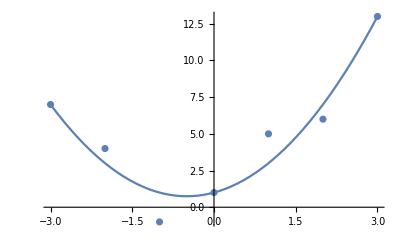

1+x+x^2

```mathematica
poly1[x_]=kvadrati[2,{-3,-2,-1,0,1,2,3},{7,4,-1,1,5,6,13}]
```

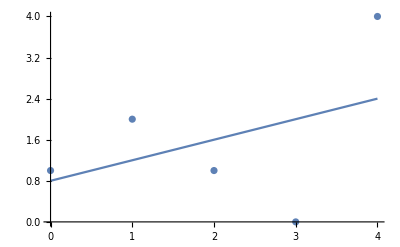

4/5+(2 x)/5

```mathematica
poly2[x_]=kvadrati[1,{0,1,2,3,4},{1,2,1,0,4}]
```

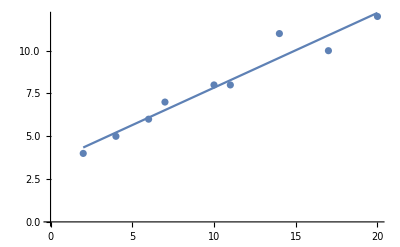

59/17+(52 x)/119

```mathematica
poly3[x_]=kvadrati[1,{2,4,6,7,10,11,14,17,20},{4,5,6,7,8,8,11,10,12}]
```

```mathematica
59/17+(52 x)/119//N
```

3.47059+0.436975 x